```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript["M","⊙"],FormatType->StandardForm];
```

```mathematica
hmf = ReadList[NotebookDirectory[]<>"HMF.dat",Table[Number,{6}]];
hmfi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[4]]}&/@hmf,InterpolationOrder->1]
dotMi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[5]]}&/@hmf,InterpolationOrder->1];
DdotMi = Interpolation[{#[[1]],#[[2]],#[[3]],#[[6]]}&/@hmf,InterpolationOrder->1];
```

7       17
InterpolatingFunction[{{0.2, 100.}, {0.01, 20.01}, {1. 10 , 1. 10  }}, <>]

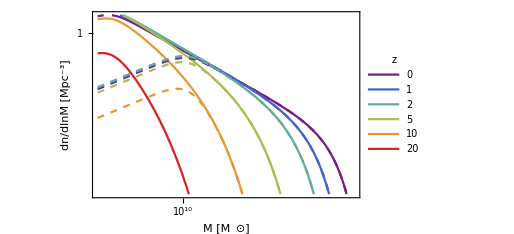

```mathematica
Show[Plot[Log10[10^9hmfi[100.0,#,10^logM]]&/@{0.01,1,2,5,10,20}//Evaluate,{logM,7,16},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [Mpc^-3]"},PlotRange->{{7,16},{-9,1}},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,5]),ImageSize->380,PlotRangePadding->None,FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotLegends->LineLegend[Automatic,{0,1,2,5,10,20},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendMarkerSize->{10,4},LegendLabel->Style["z",14]]],
Plot[Log10[10^9hmfi[1.,#,10^logM]]&/@{0.01,1,2,5,10,20}//Evaluate,{logM,7,16},PlotRange->{{7,16},{-9,1}},PlotStyle->(Directive[ColorData["Rainbow"][#],Dashed]&/@Subdivide[0,1,5])]]
```

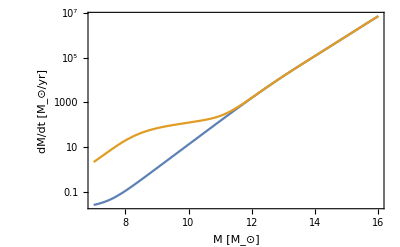

```mathematica
LogPlot[{10^-6*dotMi[100.0,4,10^logM],10^-6*dotMi[0.2,4,10^logM]},{logM,7,16},FrameLabel->{"M ["<>Msunt<>"]","dM/dt ["<>Msunt<>"/yr]"}]
```

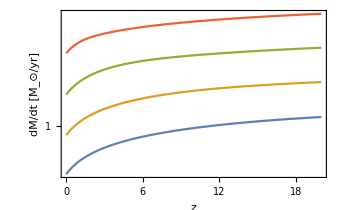

```mathematica
Plot[10^-6*dotMi[100.,z,10^#]&/@Range[8,14,2]//Log10//Evaluate,{z,0.01,20},FrameLabel->{"z","dM/dt ["<>Msunt<>"/yr]"},FrameTicks->{{logticksx,logticksx2},Automatic},ImageSize->340]
```

```mathematica
find0[X_]:=Module[{Xmax,jcut},
Xmax = First@First@MaximalBy[X,Last];
jcut = First@Flatten@Position[Select[X,#[[1]]>Xmax&],0];
X[[1;;jcut]]
]
Plnmulist = ReadList[NotebookDirectory[]<>"Plnmu.dat",Table[Number,{3}]];
zlist = DeleteDuplicates[Plnmulist[[All,1]]]
Plnmulist =GatherBy[Plnmulist,First][[All,All,{2,3}]];
Plnmui = Interpolation[find0[#],InterpolationOrder->1]&/@Plnmulist;
Plnmuf=Table[Function[lnmu,Piecewise[{{Plnmui[[j]][lnmu],Plnmui[[j]][[1,1,1]]<lnmu < Plnmui[[j]][[1,1,2]]}},0]//Evaluate],{j,Length@Plnmui}];
```

{4,5,6,7,8,9,10,11,12.5,14.5}

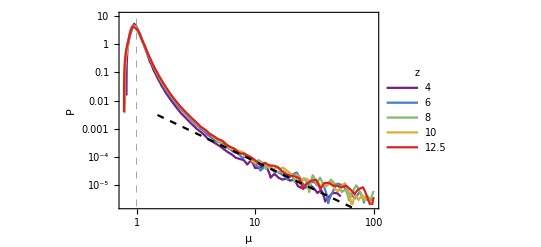

```mathematica
Show[LogLogPlot[#[Log@x]&/@Plnmuf[[1;;-1;;2]]//Evaluate,{x,0.7,100},PlotRange->{All,{2.*^-6,10}},GridLines->{{1},{}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"μ","P"},PlotStyle->(ColorData["Rainbow"][#]&/@Subdivide[0,1,4]),PlotLegends->LineLegend[Automatic,zlist[[1;;-1;;2]],LegendMarkerSize->{10,4},LabelStyle->{FontSize->12,FontFamily->"Times"},LegendLabel->Style["z",14]]],
LogLogPlot[0.007x^-2,{x,1.5,100},PlotStyle->Directive[Black,Dashed]]]
```

```mathematica
data1 = Import[NotebookDirectory[]<>"UVLF_2102.07775.txt","Table"];
DeleteDuplicates[data1[[All,1]]]
Φ1[z_]:=Select[data1,#[[1]]==z&][[All,2;;5]]
data2 = Import[NotebookDirectory[]<>"UVLF_2108.01090.txt","Table"];
DeleteDuplicates[data2[[All,1]]]
Φ2[z_]:=Select[data2,#[[1]]==z&][[All,2;;5]]
data3 = Import[NotebookDirectory[]<>"UVLF_2403.03171.txt","Table"];
DeleteDuplicates[data3[[All,1]]]
Φ3[z_]:=Select[data3,#[[1]]==z&][[All,2;;5]]
```

{4,5,6,7,8,9,10}

{4,5,6,7}

{9,10,11,12.5,14.5}

```mathematica
fB = 0.0493/0.315
```

0.156508

```mathematica
MCMCchains = Select[If[#[[-1]]=="-inf",{},Interpreter["Number"][#]]&/@StringSplit/@ReadList[NotebookDirectory[]<>"MCMCchains.dat",String],Length@#>0&];
MCMCchains[[All,1]] = MCMCchains[[All,1]]/10^11; (* Subscript[M, c] in units of 10^11 Msun *)
MCMCchains[[All,2]] = MCMCchains[[All,2]]/fB; (* factorize Subscript[f, B] from f_* *)
Length@MCMCchains
```

15652

{5.63235,0.259628,0.946461,0.308824,1.13606,10.0077,0.821905,1411.03}

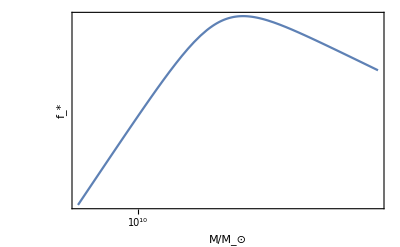
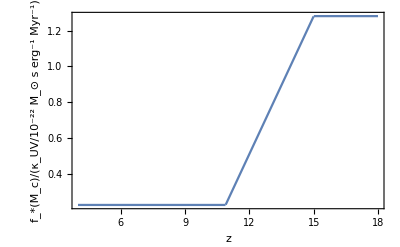

```mathematica
fstar[M_,Mc_,ϵ_,α_,β_]:=ϵ(α+β)/(β(M/Mc)^-α+α(M/Mc)^β)
First@MaximalBy[MCMCchains,Last]
Row@{Plot[Log10@fstar[10^logM,%[[1]]*10^11,%[[2]],%[[3]],%[[4]]],{logM,9,14},FrameTicks->{{logticksx,logticksx2},{logticksx,logticksx2}},PlotRange->{All,{All,0}},FrameLabel->{"M/"<>Msunt,"f_*"},ImageSize->{Automatic,240},ImagePadding->{{54,20},{40,10}}],Plot[%[[2]] Max[1,Min[%[[5]](z-%[[6]]),%[[5]](15-%[[6]])]]/1.15,{z,4,18},FrameLabel->{"z","f_*(M_c)/(κ_UV/10^-22 "<>Msunt<>" s erg^-1 Myr^-1)"},PlotRange->All,ImageSize->{Automatic,240},ImagePadding->{{54,20},{40,10}}]}
```

```mathematica
(*CP[i_,j_]:=SmoothDensityHistogram[MCMCchains[[All,{j,i}]],ImageSize->200,ImagePadding->{{50,5},{50,5}},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontSize->14,FontFamily->"Times"},ColorFunction->(Blend[{White,Orange,Red,Purple,Blue},#]&),MeshFunctions->{#3&},MeshStyle->Directive[White,Dashed],Mesh->2,FrameLabel->{Which[j==1,"M_c/10^11"<>Msunt,j==2,"ϵ",j==3,"α",j==4,"β",j==5,"γ",j==6,"z_b",j==7,"log_10m_22"],Which[i==1,"M_c/10^11"<>Msunt,i==2,"ϵ",i==3,"α",i==4,"β",i==5,"γ",i==6,"z_b",i==7,"log_10m_22"]}]
CP[i_]:=Histogram[MCMCchains[[All,i]],20,ImageSize->200,ImagePadding->{{40,4},{40,4}},AspectRatio->1,Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontSize->14,FontFamily->"Times"},FrameLabel->{Which[i==1,"M_c/10^11"<>Msunt,i==2,"ϵ",i==3,"α",i==4,"β",i==5,"γ",i==6,"z_b",i==7,"log_10m_22"],""},PlotRange->All]
Grid[Table[If[i>j,CP[i,j],If[i==j,CP[i]]],{i,Length[MCMCchains[[1]]]-1},{j,Length[MCMCchains[[1]]]-1}]]*)
```

```mathematica
UVL = ReadList[NotebookDirectory[]<>"UVluminosity.dat",Table[Number,{6}]];
zlist = UVL[[All,1]]//DeleteDuplicates
UVL = GatherBy[UVL,First][[All,All,2;;-1]];
UVLi = Table[Interpolation[UVL[[j,All,{1,5}]],InterpolationOrder->1],{j,Length@UVL}];
```

{4,5,6,7,8,9,10,11,12.5,14.5}

```mathematica
NPDF2[x_,μ_,σm_,σp_]:= 2Piecewise[{{σm PDF[NormalDistribution[μ,σm],x],x<μ}},σp PDF[NormalDistribution[μ,σp],x]]/(σm+σp)
Total@Flatten@Table[Log@NPDF2[10^9UVLi[[jz]][#[[1]]],#[[2]],#[[4]],#[[3]]]&/@Join[Φ1[zlist[[jz]]],Φ2[zlist[[jz]]],Φ3[zlist[[jz]]]],{jz,Length@zlist}]
```

1411.03

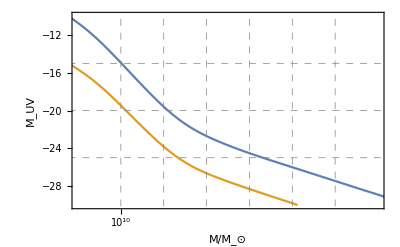

```mathematica
ListPlot[Table[{Log10@#[[2]],#[[1]]}&/@UVL[[j]],{j,{1,-1}}]//Evaluate,Joined->True,FrameLabel->{"M/"<>Msunt,"M_UV"},GridLines->{Range[10,15,1],Range[-25,-15,5]},GridLinesStyle->Directive[Gray, Dashed],PlotRange->{{9,16},{-30,-10}},FrameTicks->{Automatic,{logticksx,logticksx2}}]
```

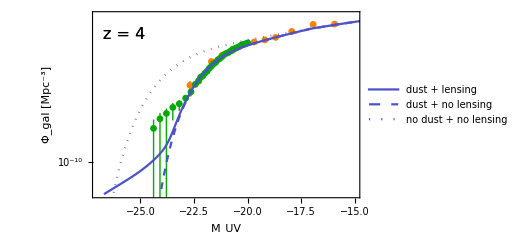

```mathematica
jz0 = 1;
Legended[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Orange,PlotRange->{{-27,-15},{-12,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->380],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Green],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Cyan],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.12,0.88}]],
ListPlot[{{#[[1]],Log10[10^9#[[3]]]}&/@UVL[[jz0]],{#[[1]],Log10[10^9#[[4]]]}&/@UVL[[jz0]],{#[[1]],Log10[10^9#[[5]]]}&/@UVL[[jz0]]}//Evaluate,PlotRange->{{-27,-15},{-12,-1}},Joined->True,PlotStyle->{Directive[RGBColor[0.3,0.32,0.78],Dotted],Directive[RGBColor[0.3,0.32,0.78],Dashed],Directive[RGBColor[0.3,0.32,0.78]]}],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.12,0.88}]]],Placed[LineLegend[{RGBColor[0.3,0.32,0.78],Directive[RGBColor[0.3,0.32,0.78],Dashed],Directive[RGBColor[0.3,0.32,0.78],Dotted]},{"dust + lensing","dust + no lensing","no dust + no lensing"},LabelStyle->{FontSize->14,FontFamily->"Times"},LegendMarkerSize->{24,4}],Scaled@{0.72,0.25}]]
```

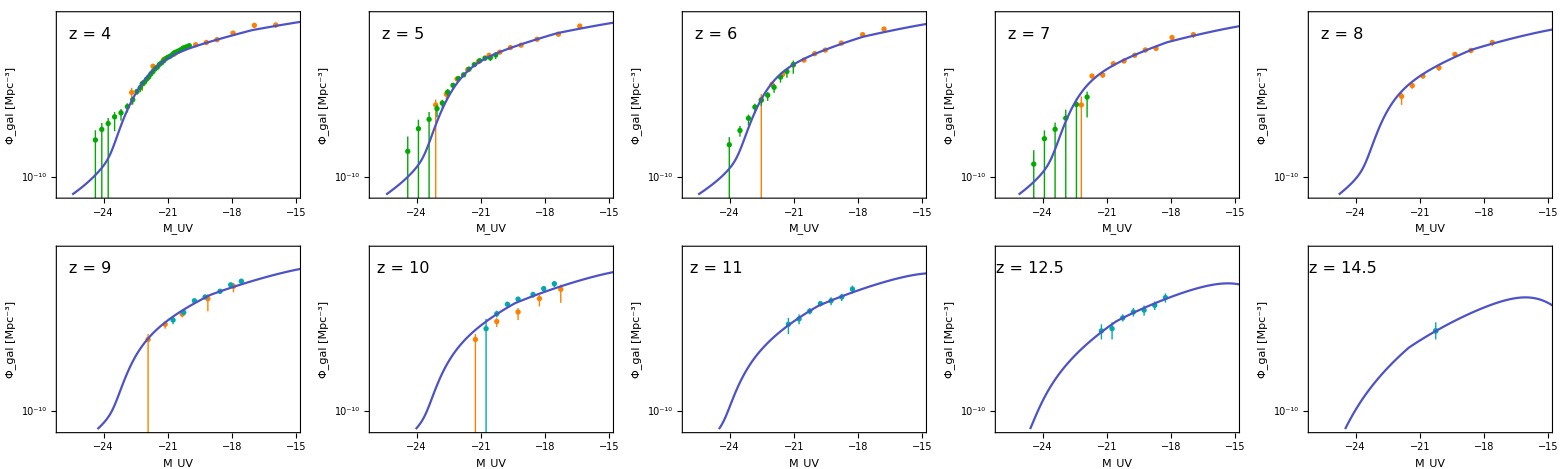

```mathematica
Grid@ArrayReshape[Table[Show[ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ1[zlist[[jz0]]]//Evaluate,PlotStyle->Orange,PlotRange->{{-26,-15},{-11,-1}},FrameLabel->{"M_UV","Φ_gal [Mpc^-3]"},FrameTicks->{{logticksx,logticksx2},Automatic},PlotStyle->DotDashed,ImageSize->300],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ2[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Green],
ListPlot[{#[[1]],Around[Log10@#[[2]],{Log10[Max[#[[2]]-#[[4]],1.*^-31]]-Log10@#[[2]],Log10[#[[2]]+#[[3]]]-Log10@#[[2]]}]}&/@Φ3[zlist[[jz0]]]//Evaluate,PlotStyle->Darker@Cyan],
ListPlot[{#[[1]],Log10[10^9#[[5]]]}&/@UVL[[jz0]]//Evaluate,PlotRange->{{-26,-15},{-11,-1}},Joined->True,PlotStyle->Directive[RGBColor[0.3,0.32,0.78]]],
Graphics[Text[Style["z = "<>ToString@zlist[[jz0]],16],Scaled@{0.14,0.88}]]],{jz0,Length@zlist}],{2,5}]
```